## Init

```mathematica
(*rotation*)
R={{1/(√2),0,0,0,0,1/(√2),0,0},{0,1/(√2),0,0,0,0,1/(√2),0},{0,0,1/2,0,0,0,0,(√3)/2},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{-1/(√2),0,0,0,0,1/(√2),0,0},{0,-1/(√2),0,0,0,0,1/(√2),0},{0,0,(-√3)/2,0,0,0,0,1/2}};
```

```mathematica
(*Definition of the f-tensor*)
f[i_,j_,k_]:=0;

f[1,2,3]=f[2,3,1]=f[3,1,2]=1;
 
f[1,3,2]=f[2,1,3]=f[3,2,1]=-1;

f[1,4,7]= f[4,7,1]=f[7,1,4]=
f[1,6,5]=f[6,5,1]=f[5,1,6]=
 f[2,4,6]= f[4,6,2]= f[6,2,4]=
f[2,5,7]=f[5,7,2]=f[7,2,5]=
 f[3,4,5]= f[4,5,3]= f[5,3,4]=
 f[3,7,6]=  f[7,6,3]= f[6,3,7]=1/2;

f[1,7,4]=f[7,4,1]=f[4,1,7]=
f[1,5,6]=f[5,6,1]=f[6,1,5]=
 f[2,6,4]= f[6,4,2]= f[4,2,6]=
f[2,7,5]=f[7,5,2]=f[5,2,7]=
 f[3,5,4]= f[5,4,3]= f[4,3,5]=
 f[3,6,7]= f[6,7,3]= f[7,3,6]=-1/2;


f[4,5,8]=f[5,8,4]=f[8,4,5]=
 f[6,7,8]= f[7,8,6]= f[8,6,7]=√3/2; 

f[4,8,5]=f[8,5,4]=f[5,4,8]=
 f[6,8,7]= f[8,7,6]= f[7,6,8]=-√3/2; 

(*Definition of the d-tensor*)

d[i_,j_,k_]=0;
d[1,1,8]=d[1,8,1]=d[8,1,1]=
d[2,2,8]=d[2,8,2]=d[8,2,2]=
d[3,3,8]=d[3,8,3]=d[8,3,3]=1/(√3);
d[8,8,8]=-1/(√3);
d[1,4,6]=d[1,6,4]=d[4,1,6]=d[4,6,1]=d[6,1,4]=d[6,4,1]=
d[1,5,7]=d[1,7,5]=d[5,1,7]=d[5,7,1]=d[7,1,5]=d[7,5,1]=
d[2,5,6]=d[2,6,5]=d[5,2,6]=d[5,6,2]=d[6,2,5]=d[6,5,2]=
d[3,4,4]=d[4,3,4]=d[4,4,3]=
d[3,5,5]=d[5,3,5]=d[5,5,3]=1/2;
d[2,4,7]=d[2,7,4]=d[4,2,7]=d[4,7,2]=d[7,2,4]=d[7,4,2]=
d[3,6,6]=d[6,3,6]=d[6,6,3]=
d[3,7,7]=d[7,3,7]=d[7,7,3]=-1/2;
d[4,4,8]=d[4,8,4]=d[8,4,4]=
d[5,5,8]=d[5,8,5]=d[8,5,5]=
d[6,6,8]=d[6,8,6]=d[8,6,6]=
d[7,7,8]=d[7,8,7]=d[8,7,7]=-1/(2 √3);
```

## Constants

```mathematica
Sites=8;
```

```mathematica
tmax=20;
```

```mathematica
Nt=128;
dt=tmax/Nt;
Length[ts=N@Range[0,tmax-dt,dt]];
```

```mathematica
times=Table[t,{t,0,tmax-dt,dt}];
```

```mathematica
Runs=1000;
mSIM=10;
```

```mathematica
Uvalue=1;
μvalue=1;
Jvalue=0.01;
navgvalue=1;
```

```mathematica
putvalues:={U->Uvalue,J->Jvalue,navg->navgvalue,μ->μvalue};
```

## QM

### Diagonalizing

```mathematica
Jx=1/(√2){{0,1,0},{1,0,1},{0,1,0}};
Jy=1/(√2){{0,-ⅈ,0},{ⅈ,0,-ⅈ},{0,ⅈ,0}};
Jz={{1,0,0},{0,0,0},{0,0,-1}};
```

```mathematica
SxBasis=Table[Normalize[Eigenvectors[Jx][[n]]],{n,1,3}];
```

```mathematica
JxS=Table[SparseArray[Flatten[Outer[Times,IdentityMatrix[3^(n-1)],Jx,IdentityMatrix[3^(Sites-n)]],{{1,3,5},{2,4,6}}]],{n,1,Sites}];
JyS=Table[SparseArray[Flatten[Outer[Times,IdentityMatrix[3^(n-1)],Jy,IdentityMatrix[3^(Sites-n)]],{{1,3,5},{2,4,6}}]],{n,1,Sites}];JzS=Table[SparseArray[Flatten[Outer[Times,IdentityMatrix[3^(n-1)],Jz,IdentityMatrix[3^(Sites-n)]],{{1,3,5},{2,4,6}}]],{n,1,Sites}];
```

```mathematica
(*HQM=Sum[U/2 JzS[[n]].JzS[[n]]-μ JzS[[n]],{n,1,Sites}]- J navg Sum[Sum[JxS[[n]].JxS[[m]]+JyS[[n]].JyS[[m]],{m,n+1,Sites}],{n,1,Sites}];*)
```

```mathematica
ProgressIndicator[Dynamic[l],{1,Sites}]
```

```mathematica
ProgressIndicator[Dynamic[n],{1,Sites}]
```

```mathematica
ProgressIndicator[Dynamic[m],{1,Sites}]
```

```mathematica
Timing[HQM=Sum[Uvalue/2 JzS[[l]].JzS[[l]]-μvalue JzS[[l]],{l,1,Sites}]- Jvalue navgvalue Sum[Sum[Flatten[Outer[Times,IdentityMatrix[3^(n-1)],Jx+Jy,IdentityMatrix[3^(m-n-1)],Jx+Jy,IdentityMatrix[3^(Sites-m)]],{{1,3,5,7,9},{2,4,6,8,10}}],{m,n+1,Sites}],{n,1,Sites}];]
```

{3722.88,Null}

```mathematica
(*Timing[{En,ψn}=Eigensystem[HQM];]*)
```

```mathematica
Timing[{En,ψn}=Eigensystem[HQM];]
```

{1720.13,Null}

```mathematica
cn=Array[c,3^Sites];
```

```mathematica
Ψ=Sum[cn[[n]] ψn[[n]] ⅇ^(-ⅈ En[[n]] t),{n,1,3^Sites}];
```

### Initial conditons

```mathematica
AvgSx[n_,time_]:=Ψ*.JxS[[n]].Ψ/.t->time;
AvgSy[n_,time_]:=Ψ*.JyS[[n]].Ψ/.t->time;
AvgSz[n_,time_]:=Ψ*.JzS[[n]].Ψ/.t->time;
```

```mathematica
szdw=Solve[Flatten[Outer[Times,{1,0,0},{0,1,0},{0,0,1},{1,0,0},{0,1,0},{0,0,1},{1,0,0},{0,0,1}]]==Sum[cn[[n]] ψn[[n]] ,{n,1,3^Sites}],cn];
```

### Plotting

```mathematica
Timing[stufftp=AvgSz[1,t]/.szdw[[1]];]
```

$Aborted

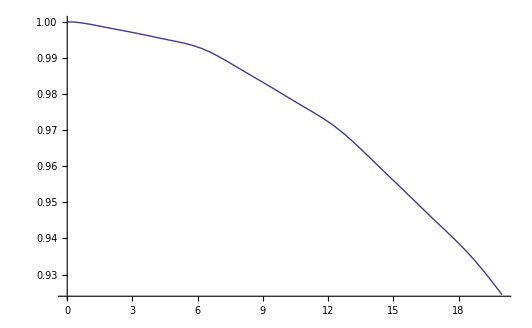
{46.9349,-Graphics-}

```mathematica
Timing[sxplus6=Plot[stufftp,{t,0,tmax},PlotRange->All]]
```

```mathematica
Save["siteone8",sxplus6]
```

```mathematica
Timing[stufftp2=AvgSz[2,t]/.szdw[[1]];]
```

{295.87,Null}

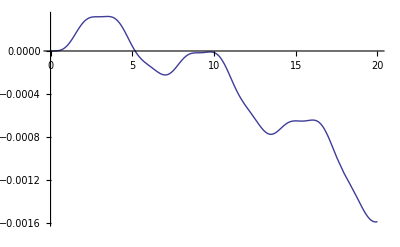
{80.1028,-Graphics-}

```mathematica
Timing[sxmiddle6=Plot[stufftp2,{t,0,tmax},PlotRange->All]]
```

```mathematica
Save["sitetwo8",sxmiddle6]
```

## Dynamic Equations

```mathematica
vν=Table[Table[ν[m,n][t],{n,1,8}],{m,1,Sites}];
dν=Table[Table[ν[m,n]'[t],{n,1,8}],{m,1,Sites}];
initialsν:=Flatten[Table[Table[ν[m,n][0]==Subscript[ν, 0][m,n],{n,1,8}],{m,1,Sites}]];
Δν[m_,ow_]:=Table[D[ow,ν[m,n][t]],{n,1,8}];
```

```mathematica
vq=Table[vν[[m]].R,{m,1,Sites}];
dq=Table[dν[[m]].R,{m,1,Sites}];
Δq[m_,ow_]:=Δν[m,ow].R;
```

```mathematica
νw[m_,ow_]:=vν[[m]] ow+ⅈ/2 Table[Sum[R[[n,a]]f[a,b,c]vq[[m,c]]Δq[m,ow][[b]],{b,1,8},{c,1,8},{a,1,8}],{n,1,8}];
νwb[m_,ow_]:=vν[[m]] ow-ⅈ/2 Table[Sum[R[[n,a]]f[a,b,c]vq[[m,c]]Δq[m,ow][[b]],{b,1,8},{c,1,8},{a,1,8}],{n,1,8}];
```

```mathematica
sxν[m_,ow_]:= 2νw[m,ow][[1]];
syν[m_,ow_]:= 2νw[m,ow][[2]];
szν[m_,ow_]:= 2νw[m,ow][[3]];
szsν[m_,ow_]:=2(-1/(√3))νw[m,ow][[8]];
sxνb[m_,ow_]:= 2νwb[m,ow][[1]];
syνb[m_,ow_]:= 2νwb[m,ow][[2]];
szνb[m_,ow_]:= 2νwb[m,ow][[3]];
szsνb[m_,ow_]:=2(-1/(√3))νwb[m,ow][[8]];
```

```mathematica
(*Hν[m_,ow_]:=U/2 szsν[m,ow]-J navg (sxν[m,ow](Sum[sxν[n,1],{n,1,m-1}]+Sum[sxν[n,1],{n,m+1,Sites}])+syν[m,ow](Sum[syν[n,1],{n,1,m-1}]+Sum[syν[n,1],{n,m+1,Sites}]))-μ szν[m,ow];
Hνb[m_,ow_]:=U/2 szsνb[m,ow]-J navg (sxνb[m,ow](Sum[sxνb[n,1],{n,1,m-1}]+Sum[sxνb[n,1],{n,m+1,Sites}])+syνb[m,ow](Sum[syνb[n,1],{n,1,m-1}]+Sum[syνb[n,1],{n,m+1,Sites}]))-μ szνb[m,ow];*)
```

```mathematica
(*eqnsν1=Table[dν[[1,n]]==Simplify[ⅈ (Hν[1,vν[[1,n]]]-Hνb[1,vν[[1,n]]])],{n,1,8}]*)
```

```mathematica
eqnsν1={ν[1,1]'[t]==μ ν[1,2][t]+1/2 U ν[1,7][t]-2 J navg ν[1,3][t] ν[2,2][t],ν[1,2]'[t]==-μ ν[1,1][t]-1/2 U ν[1,6][t]+2 J navg ν[1,3][t] ν[2,1][t],ν[1,3]'[t]==2 J navg (-ν[1,2][t] ν[2,1][t]+ν[1,1][t] ν[2,2][t]),ν[1,4]'[t]==2 (μ ν[1,5][t]+J navg (ν[1,7][t] ν[2,1][t]+ν[1,6][t] ν[2,2][t])),ν[1,5]'[t]==-2 (μ ν[1,4][t]+J navg (ν[1,6][t] ν[2,1][t]-ν[1,7][t] ν[2,2][t])),ν[1,6]'[t]==1/2 U ν[1,2][t]+μ ν[1,7][t]+2 J navg (ν[1,5][t] ν[2,1][t]-(ν[1,4][t]+√3 ν[1,8][t]) ν[2,2][t]),ν[1,7]'[t]==-1/2 U ν[1,1][t]-μ ν[1,6][t]-2 J navg (ν[1,4][t] ν[2,1][t]-√3 ν[1,8][t] ν[2,1][t]+ν[1,5][t] ν[2,2][t]),ν[1,8]'[t]==-2 √3 J navg (ν[1,7][t] ν[2,1][t]-ν[1,6][t] ν[2,2][t])};
```

```mathematica
eqnsν:=Flatten[Table[eqnsν1/.Flatten[Table[{ν[1,n]'[t]->ν[m,n]'[t],ν[1,n][t]->ν[m,n][t],ν[2,n][t]->(Sum[ν[l,n][t],{l,1,m-1}]+Sum[ν[l,n][t],{l,m+1,Sites}])},{n,1,8}]],{m,1,Sites}]];
```

```mathematica
MatrixForm[eqnsν];
```

```mathematica
eqnsν[[3]]
```

ν[1,3]'[t]==2 J navg (-ν[1,2][t] (ν[2,1][t]+ν[3,1][t]+ν[4,1][t]+ν[5,1][t]+ν[6,1][t])+ν[1,1][t] (ν[2,2][t]+ν[3,2][t]+ν[4,2][t]+ν[5,2][t]+ν[6,2][t]))

```mathematica
eqnsν[[27]]
```

ν[4,3]'[t]==2 J navg (-ν[4,2][t] (ν[1,1][t]+ν[2,1][t]+ν[3,1][t]+ν[5,1][t]+ν[6,1][t])+ν[4,1][t] (ν[1,2][t]+ν[2,2][t]+ν[3,2][t]+ν[5,2][t]+ν[6,2][t]))

```mathematica
eqnsν[[43]]
```

ν[6,3]'[t]==2 J navg ((ν[1,2][t]+ν[2,2][t]+ν[3,2][t]+ν[4,2][t]+ν[5,2][t]) ν[6,1][t]-(ν[1,1][t]+ν[2,1][t]+ν[3,1][t]+ν[4,1][t]+ν[5,1][t]) ν[6,2][t])

## Delta functions

```mathematica
szup={0,0,1/2,0,0,0,0,-1/(2 √3)};
szmiddle={0,0,0,0,0,0,0,1/(√3)};
szdown={0,0,-1/2,0,0,0,0,-1/(2 √3)};
```

```mathematica
inits=Table[0,{Sites},{8}];
```

```mathematica
inits={szup,szmiddle,szdown,szup,szmiddle,szdown};
```

```mathematica
(*inits=Table[RandomVariate[NormalDistribution[meansz0[[n]],√(varsz0[[n]]+1/8)]],{Sites},{n,1,8}];*)
```

```mathematica
νsolve=NDSolve[(eqnsν~Join~initialsν)/.{U->Uvalue,μ->μvalue,J->Jvalue,navg->navgvalue}~Join~Flatten[Table[Subscript[ν, 0][m,n]->inits[[m,n]],{m,1,Sites},{n,1,8}]],Flatten[vν],{t,0,tmax},MaxSteps->∞];
```

{{ν[1,1][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[1,2][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[1,3][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[1,4][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[1,5][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[1,6][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[1,7][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[1,8][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[2,1][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[2,2][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[2,3][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[2,4][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[2,5][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[2,6][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[2,7][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[2,8][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[3,1][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[3,2][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[3,3][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[3,4][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[3,5][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[3,6][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[3,7][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[3,8][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[4,1][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[4,2][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[4,3][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[4,4][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[4,5][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[4,6][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[4,7][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[4,8][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[5,1][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[5,2][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[5,3][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[5,4][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[5,5][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[5,6][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[5,7][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[5,8][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[6,1][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[6,2][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[6,3][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[6,4][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[6,5][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[6,6][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[6,7][t]→InterpolatingFunction[{{0.,20.}},<>][t],ν[6,8][t]→InterpolatingFunction[{{0.,20.}},<>][t]}}

```mathematica
DSolve[(eqnsν~Join~initialsν),Flatten[vν],t]
```

DSolve[{ν[1,1]'[t]==μ ν[1,2][t]+1/2 U ν[1,7][t]-4 J navg ν[1,3][t] ν[2,2][t],ν[1,2]'[t]==-μ ν[1,1][t]-1/2 U ν[1,6][t]+4 J navg ν[1,3][t] ν[2,1][t],ν[1,3]'[t]==4 J navg (-ν[1,2][t] ν[2,1][t]+ν[1,1][t] ν[2,2][t]),ν[1,4]'[t]==2 μ ν[1,5][t]+4 J navg (ν[1,7][t] ν[2,1][t]+ν[1,6][t] ν[2,2][t]),ν[1,5]'[t]==-2 μ ν[1,4][t]+4 J navg (-ν[1,6][t] ν[2,1][t]+ν[1,7][t] ν[2,2][t]),ν[1,6]'[t]==1/2 U ν[1,2][t]+μ ν[1,7][t]+4 J navg (ν[1,5][t] ν[2,1][t]-(ν[1,4][t]+√3 ν[1,8][t]) ν[2,2][t]),ν[1,7]'[t]==-1/2 U ν[1,1][t]-μ ν[1,6][t]-4 J navg (ν[1,4][t] ν[2,1][t]-√3 ν[1,8][t] ν[2,1][t]+ν[1,5][t] ν[2,2][t]),ν[1,8]'[t]==-4 √3 J navg (ν[1,7][t] ν[2,1][t]-ν[1,6][t] ν[2,2][t]),ν[2,1]'[t]==μ ν[2,2][t]-4 J navg ν[1,2][t] ν[2,3][t]+1/2 U ν[2,7][t],ν[2,2]'[t]==-μ ν[2,1][t]+4 J navg ν[1,1][t] ν[2,3][t]-1/2 U ν[2,6][t],ν[2,3]'[t]==4 J navg (ν[1,2][t] ν[2,1][t]-ν[1,1][t] ν[2,2][t]),ν[2,4]'[t]==2 μ ν[2,5][t]+4 J navg (ν[1,2][t] ν[2,6][t]+ν[1,1][t] ν[2,7][t]),ν[2,5]'[t]==-2 μ ν[2,4][t]+4 J navg (-ν[1,1][t] ν[2,6][t]+ν[1,2][t] ν[2,7][t]),ν[2,6]'[t]==1/2 U ν[2,2][t]+μ ν[2,7][t]+4 J navg (ν[1,1][t] ν[2,5][t]-ν[1,2][t] (ν[2,4][t]+√3 ν[2,8][t])),ν[2,7]'[t]==-1/2 U ν[2,1][t]-μ ν[2,6][t]-4 J navg (ν[1,1][t] ν[2,4][t]+ν[1,2][t] ν[2,5][t]-√3 ν[1,1][t] ν[2,8][t]),ν[2,8]'[t]==-4 √3 J navg (-ν[1,2][t] ν[2,6][t]+ν[1,1][t] ν[2,7][t]),ν[1,1][0]==ν_0[1,1],ν[1,2][0]==ν_0[1,2],ν[1,3][0]==ν_0[1,3],ν[1,4][0]==ν_0[1,4],ν[1,5][0]==ν_0[1,5],ν[1,6][0]==ν_0[1,6],ν[1,7][0]==ν_0[1,7],ν[1,8][0]==ν_0[1,8],ν[2,1][0]==ν_0[2,1],ν[2,2][0]==ν_0[2,2],ν[2,3][0]==ν_0[2,3],ν[2,4][0]==ν_0[2,4],ν[2,5][0]==ν_0[2,5],ν[2,6][0]==ν_0[2,6],ν[2,7][0]==ν_0[2,7],ν[2,8][0]==ν_0[2,8]},{ν[1,1][t],ν[1,2][t],ν[1,3][t],ν[1,4][t],ν[1,5][t],ν[1,6][t],ν[1,7][t],ν[1,8][t],ν[2,1][t],ν[2,2][t],ν[2,3][t],ν[2,4][t],ν[2,5][t],ν[2,6][t],ν[2,7][t],ν[2,8][t]},t]

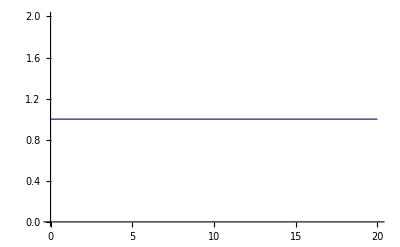
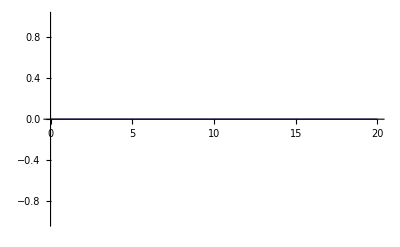
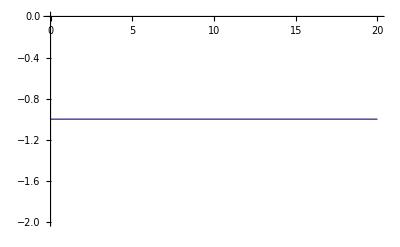

```mathematica
Table[Plot[2 ν[n,m][t]/.νsolve,{t,0,20}],{n,1,3,1},{m,3,3,1}]
```

```mathematica
Table[Plot[2 ν[n,m][t]/.νsolve,{t,0,20}],{n,4,6,1},{m,3,3,1}]
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

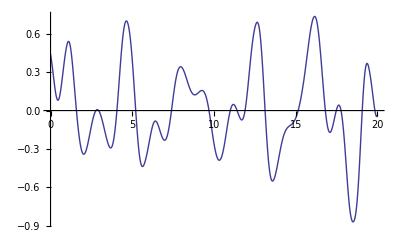
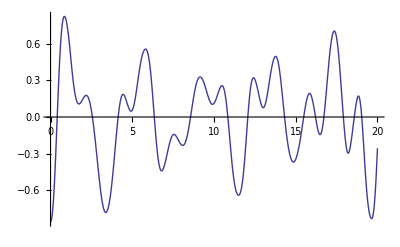
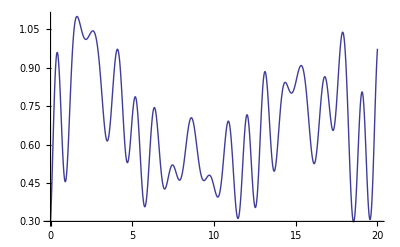
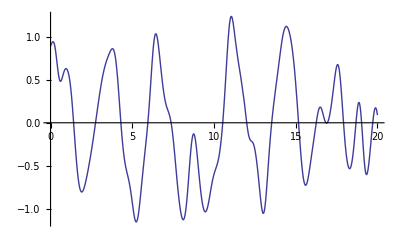
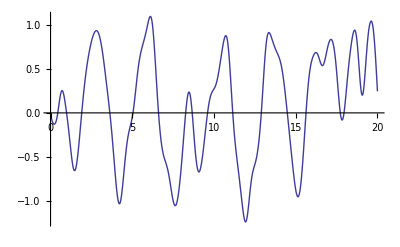
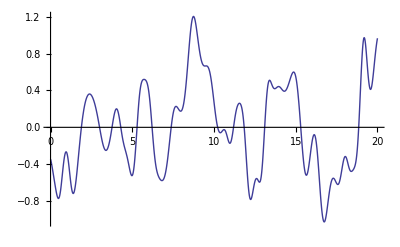
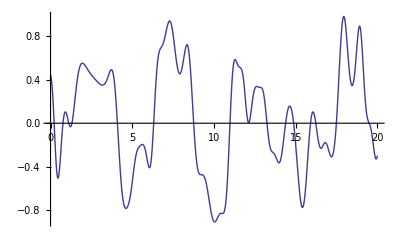
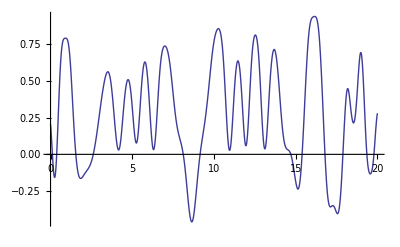

```mathematica
Table[Plot[ν[n,m][t]/.νsolve,{t,0,20}],{n,1,2,1},{m,1,8,1}]
```

```mathematica
Manipulate[Plot[ν[n,m][t]/.νsolve,{t,0,20}],{n,1,2,1},{m,1,8,1}]
```

## Gausian Wigner functions

```mathematica
meansz0={0,0,0,0,0,0,0,1/2 (1/(2 √3)+(√3)/2)};
```

```mathematica
varsz0={1/2,1/2,0,0,0,1/2,1/2,0};
```

```mathematica
meansxp1={1/2,0,0,1/4,0,0,0,1/2 (-1/(4 √3)+1/4 (1/(2 √3)-(√3)/2)+1/2 (1/(2 √3)+(√3)/2))};
varsxp1={0,1/(2 √2),1/(2 √2),1/4,1/(2 √2),1/(2 √2),1/2,√(-1/4 (-1/(4 √3)+1/4 (1/(2 √3)-(√3)/2)+1/2 (1/(2 √3)+(√3)/2))^2+1/4 (1/12+1/4 (1/(2 √3)-(√3)/2)^2+1/2 (1/(2 √3)+(√3)/2)^2))};
```

```mathematica
spindyn={};
Timing[
Do[
inits=Table[RandomVariate[NormalDistribution[meansxp1[[n]],√(varsxp1[[n]]+1/8)]],{Sites},{n,1,8}];
TWAres=
ParallelTable[
vν/.
NDSolve[
(eqnsν~Join~initialsν)/.{U->Uvalue,μ->μvalue,J->Jvalue,navg->navgvalue}~Join~Flatten[Table[Subscript[ν, 0][m,n]->inits[[m,n]],{m,1,Sites},{n,1,8}]],Flatten[vν],{t,0,tmax},MaxSteps->∞
],
{ii,mSIM}
];
spindyn=spindyn~Join~(Table[TWAres[[All,1,All,All]],{t,ts}]ᵀ)
,{j,0,(Runs/mSIM-1)}
]
]
```

{20.74731,Null}

```mathematica
avgspins=Total[spindyn]/Runs;
```

```mathematica
Dimensions[spindyn]
```

{1000,128,2,8}

```mathematica
Dimensions[avgspins]
```

{128,2,8}

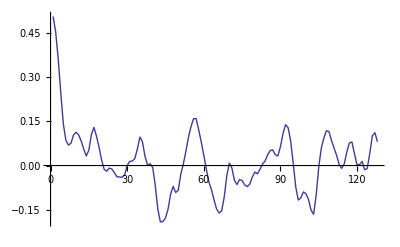

```mathematica
ListPlot[avgspins[[All,2,1]],Joined->True]
```

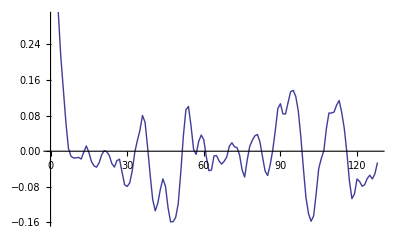

```mathematica
ListPlot[avgspins[[All,1,1]],Joined->True]
```

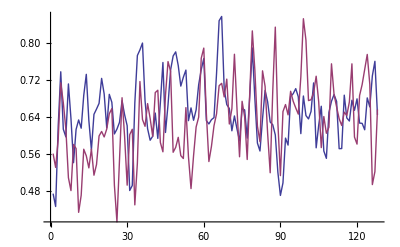

```mathematica
ListPlot[Table[2/3(1-√3 avgspins[[All,n,8]]),{n,1,2}],Joined->True]
```

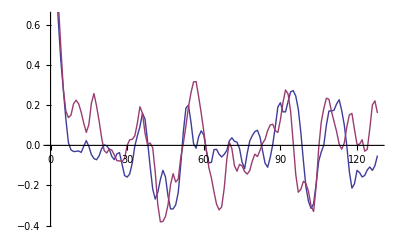

```mathematica
ListPlot[Table[2avgspins[[All,n,1]],{n,1,Sites}],Joined->True]
```

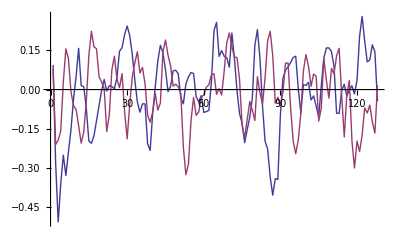

```mathematica
ListPlot[Table[2avgspins[[All,n,5]],{n,1,Sites}],Joined->True]
```

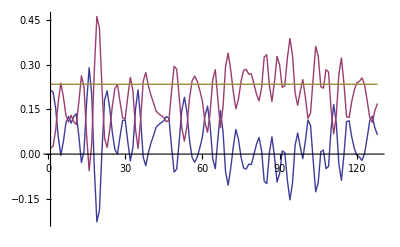

```mathematica
ListPlot[Table[2avgspins[[All,n,3]],{n,1,Sites}]~Join~{Sum[2avgspins[[All,n,3]],{n,1,Sites}]},Joined->True,PlotRange->All]
```

## SU3 Wigner with neg prob

```mathematica
Wigxplusnonorm[α_,β_,γ_]:=(-1+β* (√2 α+2 β+√2 γ)+(α+√2 β+γ) (α*+γ*));
νvarsingreek={((α+γ) Conjugate[β]+β (Conjugate[α]+Conjugate[γ]))/(2 √2),-(ⅈ (β Conjugate[α]+(-α+γ) Conjugate[β]-β Conjugate[γ]))/(2 √2),1/2 (Abs[α]^2-γ Conjugate[γ]),1/2 (γ Conjugate[α]+α Conjugate[γ]),-1/2 ⅈ (γ Conjugate[α]-α Conjugate[γ]),(-β Conjugate[α]+(-α+γ) Conjugate[β]+β Conjugate[γ])/(2 √2),(ⅈ (-(α+γ) Conjugate[β]+β (Conjugate[α]+Conjugate[γ])))/(2 √2),-(Abs[α]^2+Abs[γ]^2-2 β Conjugate[β])/(2 √3)};
```

```mathematica
Wigneg[a_]:=a 2 ⅇ^(-2 a^2)(4 a^2-1);
```

```mathematica
ends=4;
dx=10^-3;
```

```mathematica
avalues=Table[a,{a,0,ends,dx}];
```

```mathematica
randmag=RandomChoice[Table[Abs[Wigneg[a]],{a,avalues}]->avalues,{Sites,Runs}];
```

```mathematica
metric=1-2UnitStep[1/2-randmag];
```

```mathematica
randphase=RandomReal[{0,2π},{Sites,Runs}];
```

```mathematica
randrest=Table[RandomVariate[NormalDistribution[0,1/2]]+I RandomVariate[NormalDistribution[0,1/2]],{2},{Sites},{Runs}];
```

```mathematica
randupinit[n_]:={randmag[[n]] ⅇ^(ⅈ randphase[[n]]),randrest[[1,n]],randrest[[2,n]]};
randmiinit[n_]:={randrest[[1,n]],randmag[[n]] ⅇ^(ⅈ randphase[[n]]),randrest[[2,n]]};
randdoinit[n_]:={randrest[[1,n]],randrest[[2,n]],randmag[[n]] ⅇ^(ⅈ randphase[[n]])};
```

```mathematica
randinits={randupinit[1],randmiinit[2],randdoinit[3],randupinit[4],randmiinit[5],randdoinit[6]};
```

```mathematica
Dimensions[randinits]
```

{6,3,10000}

```mathematica
Histogram3D[Table[{Re[randmag[[1,n]] ⅇ^(ⅈ randphase[[1,n]])],Im[randmag[[1,n]] ⅇ^(ⅈ randphase[[1,n]])]},{n,1,Runs}]]
```

-Graphics3D-

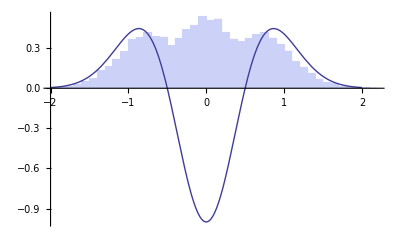

```mathematica
Show[Histogram[Table[Re[randmag[[1,n]] ⅇ^(ⅈ randphase[[1,n]])],{n,1,Runs}],{0.1},"PDF"],Plot[ⅇ^(-2 a^2)(4 a^2-1),{a,-2,2}]]
```

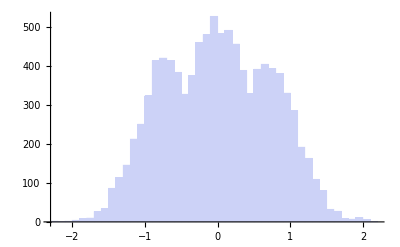

```mathematica
Histogram[Table[Re[randmag[[4,n]] ⅇ^(ⅈ randphase[[1,n]])],{n,1,Runs}],]
```

```mathematica
ProgressIndicator[Dynamic[j],{0,(Runs/mSIM-1)}]
```

```mathematica
spindyn=Table[0,{Nt},{Sites},{8}];
runsdone=0;
Timing[
Do[
TWAres=ParallelTable[
Product[metric[[n,mSIM j+ii]],{n,1,Sites}]vν/.NDSolve[(eqnsν~Join~initialsν)/.{U->Uvalue,μ->μvalue,J->Jvalue,navg->navgvalue}~Join~Flatten[Table[Subscript[ν, 0][m,n]->(νvarsingreek[[n]]/.{α->randinits[[m,1,mSIM j+ii]],β->randinits[[m,2,mSIM j+ii]],γ->randinits[[m,3,mSIM j+ii]]}),{m,1,Sites},{n,1,8}]],Flatten[vν],{t,0,tmax},MaxSteps->∞
],
{ii,mSIM}
];
spindyn=spindyn+Total[Table[TWAres[[All,1,All]],{t,ts}]ᵀ];
runsdone=runsdone+1;
,{j,0,(Runs/mSIM-1)}
]
]
avgspins=Re[spindyn]/Runs;
```

{80.97073,Null}

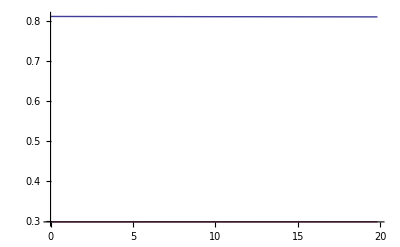

```mathematica
sx1data=ListPlot[{{times,16avgspins[[All,4,3]]}ᵀ,{times,4avgspins[[All,1,3]]}ᵀ},Joined->True,PlotRange->All]
```

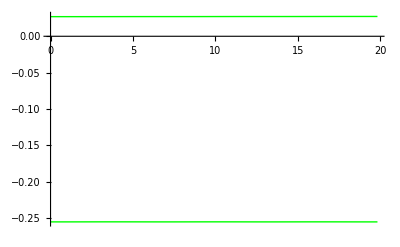

```mathematica
sx1data=ListPlot[{{times,16avgspins[[All,2,3]]}ᵀ,{times,4avgspins[[All,5,3]]}ᵀ},Joined->True,PlotRange->All, PlotStyle->Green]
```

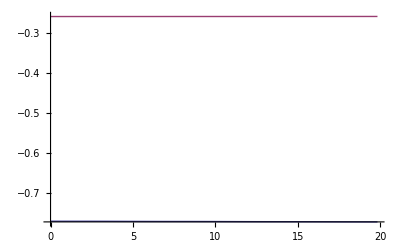

```mathematica
sx1data=ListPlot[{{times,16avgspins[[All,3,3]]}ᵀ,{times,4avgspins[[All,6,3]]}ᵀ},Joined->True,PlotRange->All]
```

## Get Wig

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/ht";
```

```mathematica
avgspins=%;
```

```mathematica
Dimensions[avgspins]
```

{128,6,8}

```mathematica
TWA6=ListPlot[{{times,2avgspins[[All,1,3]]}ᵀ,{times,2avgspins[[All,4,3]]}ᵀ},Joined->True];
```

## Plots

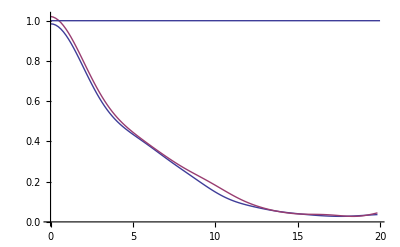

```mathematica
Show[TWA6,sxplus6]
```